numerov with  linear potential

```mathematica
(*Potential, desired max energy*)
V[s_]:=Abs[s];ϵm=20.;
(*determine grid*)
st=FindRoot[V[s]==ϵm,{s,ϵm}]⟦1,2⟧;
ds=1/√(2ϵm);
n=Round[2(st/ds+4π )];
s=Table[-ds (n+1)/2+ds i,{i,n}];
(*calculate KE matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=(one[n,-1]+10 one[n,0]+one[n,1])/12.;
A=(one[n,-1]-2 one[n,0]+one[n,1])/ds^2;
KE=-Inverse[B].A/2;
(*Hamiltonian*)
H=KE+DiagonalMatrix[V[s]];
(*Energies, wavefunctions*)
{eval,evec}=Eigensystem[H];
```

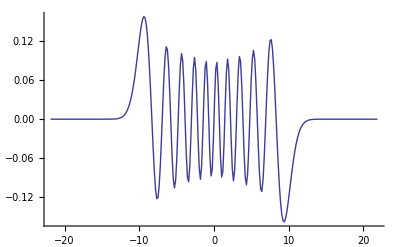

```mathematica
ListPlot[{s,evec⟦-20⟧}ᵀ,Joined->True]
```